## Лабораторная работа №5 Маевский Александр, ПО-4

## Задание 1

Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+   7
```

9

```mathematica
2/3
```

2/3

Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3      /7
```

3/7

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.          ^(1/2)
```

4.12311

Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
3                   (6 +  5 )
```

33

## Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[17^(1/2), 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[e^(x *Sqrt[163]), 40]
```

e^(12.76714533480370466171095200978089234738 x)

Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E, 100]
N[E^Pi, 100]
```

22.45915771836104547342715220454373502758931513399669224920300255406692604039911791231851975272714303

23.14069263277926900572908636794854738026610624260021199344504640952434235069045278351697199706754922

## Задание 3

Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумать свою

```mathematica
NSolve[{(12 x^5+3 y^2)/(6 y^2+5x)==4, x^3 y+y^4+x^4== 12}, {x,y}]
Length[%]
```

{{y→0.0648336-2.15212 ⅈ,x→1.21692-0.781608 ⅈ},{y→0.0648336+2.15212 ⅈ,x→1.21692+0.781608 ⅈ},{y→-1.95609+0.30585 ⅈ,x→-1.23262-0.678949 ⅈ},{y→-1.95609-0.30585 ⅈ,x→-1.23262+0.678949 ⅈ},{y→1.91796+0.376193 ⅈ,x→0.280817+1.50252 ⅈ},{y→1.91796-0.376193 ⅈ,x→0.280817-1.50252 ⅈ},{y→0.00743178+1.93522 ⅈ,x→-0.371226-1.4517 ⅈ},{y→0.00743178-1.93522 ⅈ,x→-0.371226+1.4517 ⅈ},{y→-1.91127,x→1.55108},{y→1.91224-0.0820608 ⅈ,x→-1.12123+0.761669 ⅈ},{y→1.91224+0.0820608 ⅈ,x→-1.12123-0.761669 ⅈ},{y→-0.257253-1.61462 ⅈ,x→-1.47784+0.0658167 ⅈ},{y→-0.257253+1.61462 ⅈ,x→-1.47784-0.0658167 ⅈ},{y→-0.110345+1.76888 ⅈ,x→1.135-0.672059 ⅈ},{y→-0.110345-1.76888 ⅈ,x→1.135+0.672059 ⅈ},{y→0.286099-1.54167 ⅈ,x→-0.240991-1.40483 ⅈ},{y→0.286099+1.54167 ⅈ,x→-0.240991+1.40483 ⅈ},{y→1.4031,x→1.42205},{y→-1.61079+0.0158396 ⅈ,x→0.324609+1.37013 ⅈ},{y→-1.61079-0.0158396 ⅈ,x→0.324609-1.37013 ⅈ}}

20

## Задание 4

```mathematica
FindRoot[3*Cos[x-1]== 2*Sin[x]^2, {x, -1, 3}]
```

{x→1.96813}

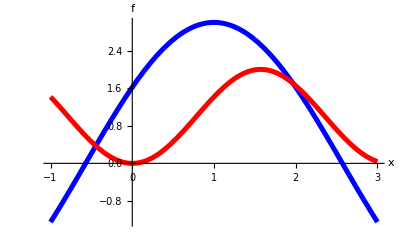

```mathematica
Plot[{3*Cos[x-1],2*Sin[x]^2}, {x, -1,3}, PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

```mathematica
FindRoot[3*Cos[x-1]== 2*Sin[x]^2, {x, -0.45}]
```

{x→-0.446281}

```mathematica
FindRoot[3*Cos[x-1]== 2*Sin[x]^2, {x, 1.95}]
```

{x→1.96813}

## Задание 5

```mathematica
sol1=NDSolve[{y''[x]-y'[x] +2*y[x]*Cos[x]^2==0, y[0]==1, y'[0]==-2},y, {x,-1,5}]
```

{{y→InterpolatingFunction[…]}}

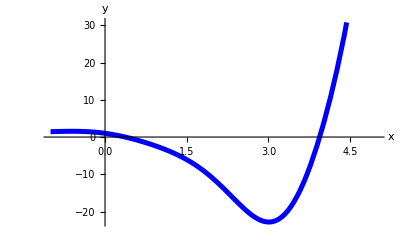

```mathematica
Plot[y[x]/.sol1, {x,-1,5}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,0.31}]
```

{x→0.368342}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2
```

-3.39049

```mathematica
sol5 = FindRoot[D[y[x]/.sol1[[1]],x]==0, {x,3}]
```

{x→3.00679}

```mathematica
y[x]/.sol1[[1]]/.sol5
```

-22.8036

```mathematica
FindMinimum[y[x]/.sol1[[1]], {x,3}]
```

{-22.8036,{x→3.00679}}

## Задание 6

```mathematica
task1 = Table[{x,(21+52x+73 x^2+17 x^3+33 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
```

{{0.,17.7306},{0.25,44.7352},{0.5,79.2917},{0.75,124.417},{1.,223.67},{1.25,335.142},{1.5,468.333},{1.75,870.245},{2.,1085.74},{2.25,1382.93},{2.5,1895.21},{2.75,3169.75},{3.,3747.22},{3.25,5312.88},{3.5,6806.61},{3.75,8271.77},{4.,8753.81},{4.25,12619.5},{4.5,15303.9},{4.75,19605.3},{5.,21613.4}}

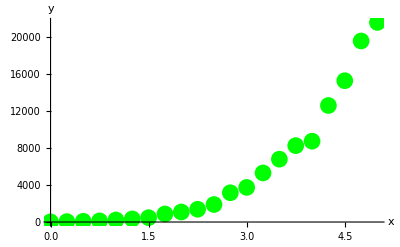

```mathematica
taskPlot=ListPlot[task1, PlotStyle->{PointSize[0.03], RGBColor[0,1,0]}, AxesLabel->{"x", "y"}]
```

```mathematica
y3=Fit[task1, {1,x,x^2, x^3, x^4},x](*-Graphics-*)
```

15.3422+106.375 x+8.37825 x^2+59.3853 x^3+22.4596 x^4

```mathematica
y4=Fit[task1, {1,x,Cos[x], Sin[x]},x]
```

-6283.55+4990.61 x+5203.01 Cos[x]-762.155 Sin[x]

```mathematica
306.355-1830.2799241963573 x+2206.498921567081 x^2-762.7871102125466 x^3+121.73760850472881 x^4
```

306.355-1830.28 x+2206.5 x^2-762.787 x^3+121.738 x^4

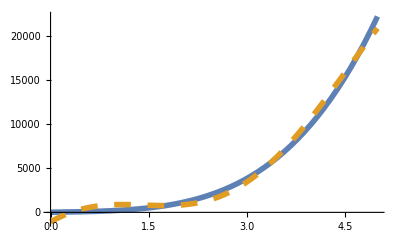

```mathematica
plot2 =Plot[{y3,y4}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
task2 = Table[{x,(21+42x+104Sin[x]+35Cos[x] +35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,90.1862},{0.25,116.916},{0.5,150.326},{0.75,159.948},{1.,176.979},{1.25,197.36},{1.5,207.462},{1.75,180.419},{2.,181.69},{2.25,155.94},{2.5,130.507},{2.75,121.536},{3.,95.1641},{3.25,84.0165},{3.5,60.8372},{3.75,56.0289},{4.,62.2615},{4.25,81.4731},{4.5,92.8455},{4.75,115.918},{5.,151.527}}

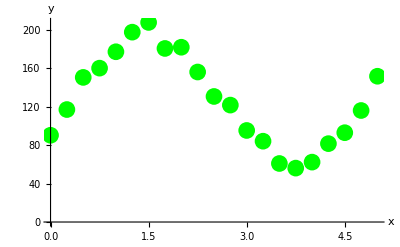

```mathematica
task2Plot=ListPlot[task2,  PlotStyle->{PointSize[0.03], RGBColor[0,1,0]}, AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

15.4816+43.8059 x+67.1136 Cos[x]+108.575 Sin[x]

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4, x^5,x^6},x]
```

91.1748+92.7208 x+53.9087 x^2-71.2985 x^3+19.1676 x^4-1.66842 x^5+0.0252133 x^6

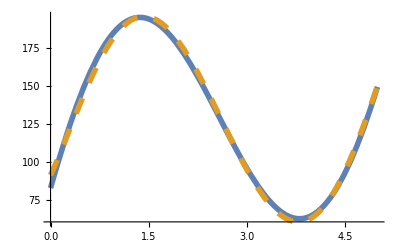

```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

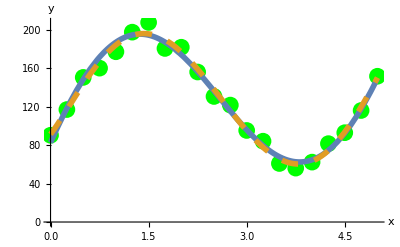

```mathematica
Show[task2Plot, plot2]
```